# Radial Coordinates for Conformal Blocks

## Conformal block expansion coefficients from the Casimir Equation:

We start with (2.21) and do the substitution as said in (2.22) to get (2.23)

```mathematica
ClearAll["Global`*"];
g[z_,zb_]:=(z*zb)^(1/2);h[z_,zb_]:=(z+zb)/(2*Sqrt[z*zb]);
m=2s*ξ;n=s^2;
Simplify[
Simplify[(((z^2(1-z)D[F[z,zb],{z,2}]-z^2D[F[z,zb],z])
+(zb^2(1-zb)D[F[z,zb],{zb,2}]-zb^2D[F[z,zb],zb])
+2ν*(z*zb/(z-zb))*((1-z)D[F[z,zb],z]
-(1-zb)D[F[z,zb],zb]))
/.F->(F[g[#1,#2],h[#1,#2]]&))
/.{z->0.5(m+Sqrt[m^2-4n]),zb->0.5(m-Sqrt[m^2-4n])}]
/.{Sqrt[s^2]->s,1/Sqrt[s^2]->1/s}]
```

(-1. s ν+0.5 ξ+1. ν ξ-0.5 s ξ^2) F^(0,1)[1. s,1. ξ]+(-0.5+0.5 s ξ+0.5 ξ^2-0.5 s ξ^3) F^(0,2)[1. s,1. ξ]+s ((-0.5-1. ν-0.5 s ξ) F^(1,0)[1. s,1. ξ]+s ((1.-1. ξ^2) F^(1,1)[1. s,1. ξ]+(0.5-0.5 s ξ) F^(2,0)[1. s,1. ξ]))

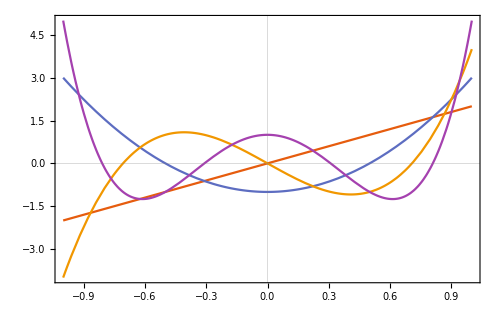

```mathematica
Plot[{GegenbauerC[1,1,x],GegenbauerC[2,1,x],GegenbauerC[3,1,x],GegenbauerC[4,1,x]},{x,-1,1},PlotTheme->"Scientific",ImageSize->500]
```

```mathematica
P[E_,j_,s_,ξ_, ν_]:=s^E Factorial[j]*GegenbauerC[j,ν,ξ]/Pochhammer[2ν,j];
```

```mathematica
D0[P_]:=s^2 D[P,{s,2}]+(2ν+1)*(ξ D[P,ξ]-s D[P,s])-(1-ξ^2)D[P,{ξ,2}]
```

```mathematica
Simplify[D0[P[En,j,s,ξ,ν]]/P[En,j,s,ξ,ν]]
```

1/GegenbauerC[j,ν,ξ](4 ν (1+ν) (-1+ξ^2) GegenbauerC[-2+j,2+ν,ξ]+2 ν (1+2 ν) ξ GegenbauerC[-1+j,1+ν,ξ]+En (En-2 (1+ν)) GegenbauerC[j,ν,ξ])

Take derivative of equation 14 and use equation 16 as it is in ‘http://mathworld.wolfram.com/GegenbauerPolynomial.html’ to get (25).

```mathematica
D1[P_]:=s(-ξ*s^2 D[P,{s,2}] +2*(1-ξ^2)s*D[D[P,s],ξ] -ξ*s D[P,s] - (2ν+ξ^2) D[P,ξ] + ξ(1-ξ^2) D[P,{ξ,2}]);
```

```mathematica
Simplify[D1[P[En,j,s,ξ,ν]]]
```

-1/Pochhammer[2 ν,j]s^(1+En) j! (4 ν (1+ν) ξ (-1+ξ^2) GegenbauerC[-2+j,2+ν,ξ]+2 ν (2 ν+ξ^2+2 En (-1+ξ^2)) GegenbauerC[-1+j,1+ν,ξ]+En^2 ξ GegenbauerC[j,ν,ξ])

## Recursion relations:

```mathematica
Ei[Δ_,j_]:=Δ(Δ-2-2ν)+j(j+2ν);
GammaPlus[En_,j_]:=(En+j)^2 (j+2ν)/(2(j+ν))
GammaMinus[En_,j_]:=(En-j-2ν)^2 j/(2(j+ν))
```

```mathematica
A[n_,j_,l_]:=If[n==0 ,If[j==l,1,0],
(GammaPlus[Δ+n-1,j-1]A[n-1,j-1,l]-GammaMinus[Δ+n-1,j+1]A[n-1,j+1,l])/(Ei[Δ+n,j] - Ei[Δ,l]  )]
```

Reproducing (2.30)

```mathematica
{Simplify[A[1,l-1,l]],Simplify[A[1,l+1,l]],Simplify[A[2,l+2,l]],Simplify[A[2,l,l]],Simplify[A[2,l-2,l]]}
```

{(l (l-Δ+2 ν))/(4 (l+ν)),((l+Δ) (l+2 ν))/(4 (l+ν)),((l+Δ) (2+l+Δ)^2 (l+2 ν) (1+l+2 ν))/(32 (1+l+Δ) (l+ν) (1+l+ν)),((l+Δ) (l-Δ+2 ν) (Δ (-1+l^2+ν+2 l ν)-ν (-2+l^2+2 ν+2 l ν)))/(16 (Δ-ν) (-1+l+ν) (1+l+ν)),((-1+l) l (2-l+Δ-2 ν)^2 (l-Δ+2 ν))/(32 (-1+l+ν) (l+ν) (-1+l-Δ+2 ν))}

## Radial coordinates:

Using the radial coordinates and requiring the agreement in the cross ratios, we see that

```mathematica
ρ= r Cos[η]+ⅈ r Sin[η];
z=4ρ/(1+ρ)^2;

s2=FullSimplify[ComplexExpand[Abs[z]]]/.{Cos[η]->η,Sqrt[r^2]->r}
ξ2=FullSimplify[ComplexExpand[(z+Conjugate[z])/(2s2)]]/.{Cos[η]->η,Sqrt[r^2]->r}
```

(4 r)/(1+r^2+2 r η)

(2 r+(1+r^2) η)/(1+r^2+2 r η)

These expressions match (3.4)

```mathematica
D1new[P_]:=4r^2((((1-2η^2+r^2)/(1+r^4-2r^2(2η^2 -1)))-(  ν/(1-r^2)))r D[P,r]+ (2η(1-η^2)/(1+r^4-2r^2(2η^2 -1)))D[P,η])
```

```mathematica
aminus[j_,ν_]:=j(j-1)/(2(j+ν)(j+ν-1));
azero[j_,ν_]:=-ν(ν-1)/((j+ν+1)(j+ν-1));
aplus[j_,ν_]:=(j+2ν+1)(j+2ν)/(2(j+ν+1)(j+ν));
bminus[j_,ν_]:=j(j-1)(j+2ν )/(2(j+ν)(j+ν-1));
bzero[j_,ν_]:=j*ν(2ν+j)/((j+ν+1)(j+ν-1));
bplus[j_,ν_]:=-(j+2ν+1)(j+2ν)j/(2(j+ν+1)(j+ν));
```

Here we define function MSimplify NSimplify and RSimplify which give the result of applying first identity, second identity and multiplying by r^2 respectively.

```mathematica
MSimplify[term_]:=term/.{P[a_,b_]->(aminus[b,ν]*P[a,b-2]+azero[b,ν]*P[a,b]+aplus[b,ν]*P[a,b+2])}
NSimplify[term_]:=term/.{P[a_,b_]->bminus[b,ν]*P[a,b-2]+bzero[b,ν]*P[a,b]+bplus[b,ν]*P[a,b+2]};
RSimplify[term_]:=Simplify[c^2*(term/.{P[a_,b_]-> c^a  d^b})]
MSimplify[term_,times_]:=Nest[MSimplify,term,times];
RSimplify[term_,times_]:=Nest[RSimplify,term,times];
```

To illustrate the utility of FindCoeff, we demonstrate the r^2 M multiplied by P[En,j].

```mathematica
FindCoeff[term_,En_,j_,a_,b_]:=Coefficient[Coefficient[term/.{P[q_,k_]-> c^q d^k}/.{d^j->1,d^(j+pat_)->d^pat},d,b]/.{c^En->1,c^(En+pat_)->c^pat},c,a];
RSimplify[MSimplify[P[En,j]]]
FindCoeff[RSimplify[MSimplify[P[En,j]]],En,j,2,2]
FindCoeff[RSimplify[MSimplify[P[En,j]]],En,j,2,-2]
FindCoeff[RSimplify[MSimplify[P[En,j]]],En,j,2,0]
```

1/2 c^(2+En) d^j (((-1+j) j)/(d^2 (-1+j+ν) (j+ν))-(2 (-1+ν) ν)/((-1+j+ν) (1+j+ν))+(d^2 (j+2 ν) (1+j+2 ν))/((j+ν) (1+j+ν)))

((j+2 ν) (1+j+2 ν))/(2 (j+ν) (1+j+ν))

((-1+j) j)/(2 (-1+j+ν) (j+ν))

-((-1+ν) ν)/((-1+j+ν) (1+j+ν))

```mathematica
RMNSimplify[term_,rtimes_,mtimes_,ntimes_]:=Nest[RSimplify,Nest[MSimplify,Nest[NSimplify,term,ntimes],mtimes],rtimes]
```

```mathematica
ExpansionCoefficients1=CoefficientList[Series[-4 r^2En((r^2 -M)/(1+r^4-2 M r^2) -ν /(1-r^2)),{r,0,10}],r^2]
ExpansionCoefficients2=CoefficientList[Series[-4r^2(1/(1+r^4-2 r^2(M))),{r,0,10}],r^2]
```

{0,4 En M+4 En ν,-4 En+8 En M^2+4 En ν,-12 En M+16 En M^3+4 En ν,4 En-32 En M^2+32 En M^4+4 En ν,20 En M-80 En M^3+64 En M^5+4 En ν}

{0,-4,-8 M,4-16 M^2,16 M-32 M^3,-4+48 M^2-64 M^4}

```mathematica
MList={};
For[i=0,i<6,i++,If[i==0,AppendTo[MList,P[En,j]],AppendTo[MList,MSimplify[Last[MList]]]]];
MList
MNList={};
For[i=0,i<6,i++,If[i==0,AppendTo[MNList,NSimplify[P[En,j]]],AppendTo[MNList,MSimplify[Last[MNList]]]]];
MNList
```

{P[En,j],4,((-1+j) j (1/1-1+1))/(2 (-1+j+ν) (j+ν))-1/((1) 1)+1/(2 (j+ν) (1+j+ν))}
 |  |  |  |

{((-1+j) j (j+2 ν) P[En,-2+j])/(2 (-1+j+ν) (j+ν))+(j ν 1 P[En,j])/((1) 1)+(j (-1-j-2 ν) (j+1) P[En,2+j])/(2 (j+ν) (1+j+ν)),4,1}
 |  |  |  |

```mathematica
a1=Table[Sum[CoefficientList[ExpansionCoefficients1[[k]],M][[i]]*MList[[i]],{i,1,k,1}],{k,2,6}]
```

{4 En ν P[En,j]+4 En (((-1+j) j P[En,1])/(2 (-1+j+ν) (j+ν))-1/((1) 1)+1/(2 (j+ν) (1+j+ν))),3,1}
 |  |  |  |

```mathematica
a2=Table[Sum[CoefficientList[ExpansionCoefficients2[[k]],M][[i]]*MNList[[i]],{i,1,k-1,1}],{k,2,6}]
```

{1}
 |  |  |  |

```mathematica
a=a1+a2
```

{4 En ν P[En,j]-4 (1)+4 En (((-1+j) j P[En,1])/(2 (-1+j+ν) (j+ν))-1/((1) 1)+1/(2 (j+ν) (1+j+ν))),3,1}
 |  |  |  |

```mathematica
gamma[arg1_,arg2_,arg3_,arg4_]:=Simplify[FindCoeff[a[[arg1-arg3-1]],arg3,arg4,0,arg2-arg4]];
gamma[En+2,j+2,En,j]
Simplify[4 (En aplus[j,ν ]-bplus[j,ν ])]
gamma[En+2,j,En,j]
Simplify[4 (En (azero[j,ν ]+ν )-bzero[j,ν ])]
gamma[En+2,j-2,En,j]
Simplify[4 (En aminus[j,ν ]-bminus[j,ν ])]
```

(2 (En+j) (j+j^2+4 j ν+2 ν (1+2 ν)))/((j+ν) (1+j+ν))

(2 (En+j) (j+j^2+4 j ν+2 ν (1+2 ν)))/((j+ν) (1+j+ν))

(4 ν ((-1+En) j^2+2 (-1+En) j ν+En (-1+ν) ν))/((-1+j+ν) (1+j+ν))

(4 ν ((-1+En) j^2+2 (-1+En) j ν+En (-1+ν) ν))/((-1+j+ν) (1+j+ν))

-(2 (-1+j) j (-En+j+2 ν))/((-1+j+ν) (j+ν))

-(2 (-1+j) j (-En+j+2 ν))/((-1+j+ν) (j+ν))

```mathematica
Simplify[(gamma[En+2,j,En,j]/.{En-> Δ,j->l})/(Ei[Δ+2,l] -Ei[Δ,l] )]
```

(ν (l^2 (-1+Δ)+2 l (-1+Δ) ν+Δ (-1+ν) ν))/((Δ-ν) (-1+l+ν) (1+l+ν))

```mathematica
Simplify[(gamma[En+2,j-2,En,j]/.{En-> Δ,j->l})/(Ei[Δ+2,l-2] -Ei[Δ,l] )]
```

((-1+l) l (l-Δ+2 ν))/(2 (-1+l+ν) (l+ν) (-1+l-Δ+2 ν))

```mathematica
Simplify[(gamma[En+2,j+2,En,j]/.{En-> Δ,j->l})/(Ei[Δ+2,l+2] -Ei[Δ,l] )]
```

((l+Δ) (l+l^2+4 l ν+2 ν (1+2 ν)))/(2 (1+l+Δ) (l+ν) (1+l+ν))

```mathematica
B[n_,k_,Δ_,l_]:= 

If[n==0,If[k-l==0,1,0],(1/(Ei[Δ+n,k]-Ei[Δ,l]))*Sum[Sum[(If[B[n1,j1,Δ,l]≠0,gamma[En+n,j,En+n1,j1]/.{En->Δ,j->l},0])*B[n1,j1,Δ,l],{j1,l-n,l+n,2}],{n1,0,n-2,2}]]
```

```mathematica
Together[(Simplify[((-1+l) l (l-Δ+2 ν))/(2 (-1+l+ν) (l+ν) (-1+l-Δ+2 ν))*gamma[En+2,j+2,En,j]/.{En->Δ+2,j-> l-2}]+Simplify[(ν (l^2 (-1+Δ)+2 l (-1+Δ) ν+Δ (-1+ν) ν))/((Δ-ν) (-1+l+ν) (1+l+ν))*gamma[En+2,j,En,j]/.{En->Δ+2,j->l}]+Simplify[((l+Δ) (l+l^2+4 l ν+2 ν (1+2 ν)))/(2 (1+l+Δ) (l+ν) (1+l+ν))* gamma[En+2,j-2,En,j]/.{En->Δ+2,j->l+2}]+gamma[En+4,j,En,j]/.{En->Δ,j->l})/(Ei[Δ+4,l]-Ei[Δ,l])]
```

(36 l^2 Δ-49 l^4 Δ+14 l^6 Δ-l^8 Δ+36 l^2 Δ^2-49 l^4 Δ^2+14 l^6 Δ^2-l^8 Δ^2-36 Δ^3+49 l^2 Δ^3-14 l^4 Δ^3+l^6 Δ^3-36 Δ^4+49 l^2 Δ^4-14 l^4 Δ^4+l^6 Δ^4-36 l^2 ν+49 l^4 ν-14 l^6 ν+l^8 ν+72 l Δ ν-134 l^2 Δ ν-196 l^3 Δ ν+176 l^4 Δ ν+84 l^5 Δ ν-46 l^6 Δ ν-8 l^7 Δ ν+4 l^8 Δ ν+60 Δ^2 ν+72 l Δ^2 ν-65 l^2 Δ^2 ν-196 l^3 Δ^2 ν-8 l^4 Δ^2 ν+84 l^5 Δ^2 ν+15 l^6 Δ^2 ν-8 l^7 Δ^2 ν-2 l^8 Δ^2 ν+102 Δ^3 ν+98 l Δ^3 ν-128 l^2 Δ^3 ν-56 l^3 Δ^3 ν+28 l^4 Δ^3 ν+6 l^5 Δ^3 ν-2 l^6 Δ^3 ν-30 Δ^4 ν+98 l Δ^4 ν+48 l^2 Δ^4 ν-56 l^3 Δ^4 ν-20 l^4 Δ^4 ν+6 l^5 Δ^4 ν+2 l^6 Δ^4 ν-72 l ν^2+98 l^2 ν^2+196 l^3 ν^2-55 l^4 ν^2-84 l^5 ν^2+6 l^6 ν^2+8 l^7 ν^2-l^8 ν^2-24 Δ ν^2-268 l Δ ν^2-204 l^2 Δ ν^2+704 l^3 Δ ν^2+161 l^4 Δ ν^2-276 l^5 Δ ν^2-35 l^6 Δ ν^2+32 l^7 Δ ν^2+2 l^8 Δ ν^2-230 Δ^2 ν^2-130 l Δ^2 ν^2+39 l^2 Δ^2 ν^2-32 l^3 Δ^2 ν^2+37 l^4 Δ^2 ν^2+90 l^5 Δ^2 ν^2+8 l^6 Δ^2 ν^2-16 l^7 Δ^2 ν^2-2 l^8 Δ^2 ν^2-30 Δ^3 ν^2-256 l Δ^3 ν^2+61 l^2 Δ^3 ν^2+112 l^3 Δ^3 ν^2+7 l^4 Δ^3 ν^2-12 l^5 Δ^3 ν^2-2 l^6 Δ^3 ν^2-4 Δ^4 ν^2+96 l Δ^4 ν^2+39 l^2 Δ^4 ν^2-80 l^3 Δ^4 ν^2-17 l^4 Δ^4 ν^2+12 l^5 Δ^4 ν^2+2 l^6 Δ^4 ν^2+196 l ν^3+76 l^2 ν^3-220 l^3 ν^3-87 l^4 ν^3+36 l^5 ν^3+15 l^6 ν^3-8 l^7 ν^3+164 Δ ν^3-16 l Δ ν^3+632 l^2 Δ ν^3+84 l^3 Δ ν^3-538 l^4 Δ ν^3-98 l^5 Δ ν^3+86 l^6 Δ ν^3+16 l^7 Δ ν^3+340 Δ^2 ν^3+470 l Δ^2 ν^3-573 l^2 Δ^2 ν^3-412 l^3 Δ^2 ν^3+291 l^4 Δ^2 ν^3+160 l^5 Δ^2 ν^3-50 l^6 Δ^2 ν^3-16 l^7 Δ^2 ν^3+150 Δ^3 ν^3+234 l Δ^3 ν^3-190 l^2 Δ^3 ν^3-12 l^3 Δ^3 ν^3+50 l^4 Δ^3 ν^3-12 l^5 Δ^3 ν^3-4 l^6 Δ^3 ν^3+90 Δ^4 ν^3+190 l Δ^4 ν^3-122 l^2 Δ^4 ν^3-108 l^3 Δ^4 ν^3+26 l^4 Δ^4 ν^3+12 l^5 Δ^4 ν^3-240 l ν^4-16 l^2 ν^4+212 l^3 ν^4-27 l^4 ν^4-22 l^5 ν^4-7 l^6 ν^4-424 Δ ν^4-144 l Δ ν^4+580 l^2 Δ ν^4-312 l^3 Δ ν^4-272 l^4 Δ ν^4+68 l^5 Δ ν^4+50 l^6 Δ ν^4-444 Δ^2 ν^4-1082 l Δ^2 ν^4-219 l^2 Δ^2 ν^4+564 l^3 Δ^2 ν^4+359 l^4 Δ^2 ν^4-76 l^5 Δ^2 ν^4-54 l^6 Δ^2 ν^4-362 Δ^3 ν^4-604 l Δ^3 ν^4+36 l^2 Δ^3 ν^4+280 l^3 Δ^3 ν^4-18 l^4 Δ^3 ν^4-24 l^5 Δ^3 ν^4-34 Δ^4 ν^4-84 l Δ^4 ν^4-150 l^2 Δ^4 ν^4+24 l^3 Δ^4 ν^4+30 l^4 Δ^4 ν^4+408 l ν^5+196 l^2 ν^5-348 l^3 ν^5-66 l^4 ν^5+70 l^5 ν^5+514 Δ ν^5+1216 l Δ ν^5-354 l^2 Δ ν^5-584 l^3 Δ ν^5+12 l^4 Δ ν^5+76 l^5 Δ ν^5+610 Δ^2 ν^5+610 l Δ^2 ν^5+342 l^2 Δ^2 ν^5+220 l^3 Δ^2 ν^5-62 l^4 Δ^2 ν^5-100 l^5 Δ^2 ν^5+290 Δ^3 ν^5+112 l Δ^3 ν^5+330 l^2 Δ^3 ν^5+8 l^3 Δ^3 ν^5-60 l^4 Δ^3 ν^5+38 Δ^4 ν^5-68 l Δ^4 ν^5+6 l^2 Δ^4 ν^5+40 l^3 Δ^4 ν^5-256 l ν^6-410 l^2 ν^6+32 l^3 ν^6+186 l^4 ν^6-286 Δ ν^6-820 l Δ ν^6-416 l^2 Δ ν^6+192 l^3 Δ ν^6+54 l^4 Δ ν^6-452 Δ^2 ν^6-204 l Δ^2 ν^6+64 l^2 Δ^2 ν^6-40 l^3 Δ^2 ν^6-110 l^4 Δ^2 ν^6-158 Δ^3 ν^6+68 l Δ^3 ν^6+42 l^2 Δ^3 ν^6-80 l^3 Δ^3 ν^6-24 Δ^4 ν^6-4 l Δ^4 ν^6+30 l^2 Δ^4 ν^6-28 l ν^7+100 l^2 ν^7+128 l^3 ν^7+46 Δ ν^7+160 l Δ ν^7+270 l^2 Δ ν^7+8 l^3 Δ ν^7+102 Δ^2 ν^7+200 l Δ^2 ν^7-38 l^2 Δ^2 ν^7-72 l^3 Δ^2 ν^7+38 Δ^3 ν^7+36 l Δ^3 ν^7-60 l^2 Δ^3 ν^7-2 Δ^4 ν^7+12 l Δ^4 ν^7-8 l ν^8-8 l^2 ν^8+14 Δ ν^8-4 l Δ ν^8-10 l^2 Δ ν^8+22 Δ^2 ν^8-28 l Δ^2 ν^8-26 l^2 Δ^2 ν^8+10 Δ^3 ν^8-24 l Δ^3 ν^8+2 Δ^4 ν^8-4 Δ ν^9-4 l Δ ν^9-8 Δ^2 ν^9-4 l Δ^2 ν^9-4 Δ^3 ν^9)/(4 (1+l+Δ) (1-l+Δ-2 ν) (Δ-ν) (1+Δ-ν) (-3+l+ν) (-2+l+ν) (-1+l+ν) (1+l+ν) (2+l+ν) (3+l+ν))

```mathematica
gamma[En+4,j,En,j]/.{En->Δ,j->l}
```

(4 ν (-l (l^5+8 ν+6 l^4 ν+34 ν^3+6 ν^5-4 l^2 ν (5+4 ν^2)+l^3 (-5+6 ν^2)+l (4-3 ν^2-21 ν^4))+Δ (-24+l^6-40 ν+6 l^5 ν+100 ν^2-31 ν^3-5 ν^4-ν^5+ν^6+4 l^3 ν (-11-3 ν+5 ν^2)+l^4 (-11-3 ν+15 ν^2)+2 l ν (34+27 ν-46 ν^2+6 ν^3+3 ν^4)+l^2 (34+27 ν-90 ν^2-6 ν^3+15 ν^4))))/((-3+l+ν) (-2+l+ν) (-1+l+ν) (1+l+ν) (2+l+ν) (3+l+ν))